```mathematica
Needs["VariationalMethods`"]
```

```mathematica
Block[
{f,m,q},
m=(1/zp^4)+8Pi l^2μ^2( 1/zp^2)(1-Sqrt[1-4λ])/3/λ;
q=(k /zp^2) l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m z^4+q^2 z^6)]);
EulerEquations[q1 μ(1-z[t]^2/zp^2)-1/z[t]Sqrt[(1+Sqrt[1-4λ])/2 f[z[t]]-z'[t]^2/f[z[t]]],z[t],t]
]
```

-(2 q1 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-((1+√(1-4 λ)) (-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))/(12 l^2 λ)+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+(√(-((1+√(1-4 λ)) (-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))/(12 l^2 λ)+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/z[t]^2-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √((3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4) (-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √((3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4) (-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))))+(6 l^2 λ z''[t])/(z[t] (-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)) √(-((1+√(1-4 λ)) (-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))/(12 l^2 λ)+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)) (-((1+√(1-4 λ)) (-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))/(12 l^2 λ)+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0

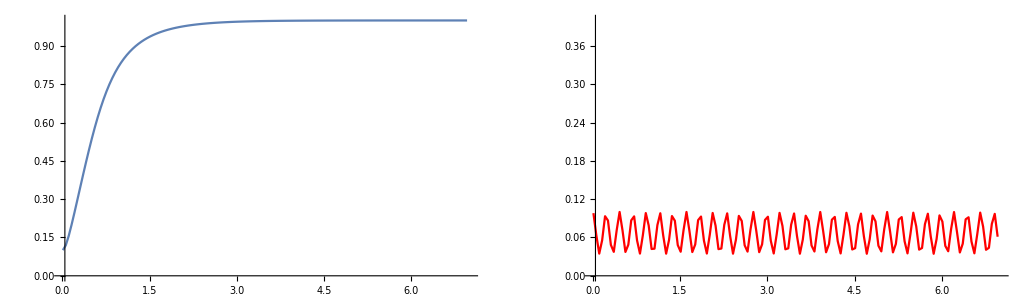

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1+4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q->q1,rp->1/zp1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,9},Method->"BDF"
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
GraphicsRow[
{
ListLinePlot[Table[{i,Abs[fz1[i,0,1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]},{i,0.01,7,0.05}],PlotRange->{{0.01,7},{0,1}}],
ListLinePlot[Table[{i,Abs[fz1[i,200qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]},{i,0.01,7,0.05}],PlotStyle->Red,PlotRange->{{0.01,7},{0,0.4}}]
}
]
]
```

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)/((1+Sqrt[1+4λ])/2);
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 k l √((1-√(1-4 λ))/λ) μ^2 z[t])/(√3 zp^4)+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q->q1,rp->1/zp1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,9},Method->"BDF"
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
GraphicsRow[
{
ListLinePlot[Table[{i,Abs[fz1[i,10qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]]},{i,0.01,6,0.05}],PlotStyle->Blue,PlotRange->{{0.01,6},{0,1}}],ListLinePlot[Table[{i,Abs[fz1[i,10qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]},{i,0.01,6,0.05}],PlotStyle->Red,PlotRange->{{0.01,6},{0,1}}],
ListLinePlot[Table[{i,Abs[fz1[i,10qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.0625],1,0.0625,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.0625],1,0.0625]]},{i,0.01,6,0.05}],PlotStyle->Orange,PlotRange->{{0.01,6},{0,1}}],
ListLinePlot[Table[{i,Abs[fz1[i,10qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875]]},{i,0.01,6,0.05}],PlotStyle->Brown,PlotRange->{{0.01,6},{0,1}}],
ListLinePlot[Table[{i,Abs[fz1[i,10qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.2],1,0.2,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.2],1,0.2]]},{i,0.01,6,0.05}],PlotStyle->Purple,PlotRange->{{0.01,6},{0,1}}]
}
]
]
```

NDSolveValue::mxst: Maximum number of 97883 steps reached at the point t == 6.83348.

General::stop: Further output of NDSolveValue::mxst will be suppressed during this calculation.

$Aborted

```mathematica
Block[
{f,m,q,qcrit},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)/((1+Sqrt[1+4λ])/2);
qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125,Sqrt[8Pi]]
]
```

45.1564